load xlr8r

```mathematica
<<xlr8r.m
```

xCellerator 0.90 (26-Oct-2012) loaded Fri 2 Nov 2012 14:22:17
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

define a model

It might help to open the xCellerator palette (from the Palettes menu, above)

This is a model of a simple enzymatic transition that is initiated by an input signal “input” and the product is degraded at a constant rate d.

```mathematica
m={{Overscript[S⇄P, X],k1,k2,k3}, 
{P->∅,d}, 
{input⇄S, k3,k4}
}
```

{{(S⇄P)^X,k1,k2,k3},{P→∅,d},{input⇄S,k3,k4}}

Test the model by running a simulation. 

All parameters that are not set will default to a value of 1.  In the following simulation, the parameter d=0 but all other parameters such as k1,k2, k3,k4 are automatically set to 1. This is useful for testing a model, but eventually you will have to tune your parameters to the correct values.

All initial conditions (values of variables such as S, P, X, etc at t=0) will default to zero. In the following simulation, the initical value of “input” and “X” are 1, and the initial values of S and P are both zero, since they are not specified.

When running your own simulations you should take special care here to make sure that the units of all of your parameters and initial conditions are consistent, e.g., if you mix nanoMoles with microMoles, make sure to apply to appropriate conversion factors to your values. 

We use the frozen option to keep the enzyme X fixed. This can also be done by adding a reaction {∅⇄X,kf,kr} with kf/kr set to the desired steady state value. However, if we use the reaction, we will have to wait for the reaction to reach steady state; the frozen option puts it there immediately.

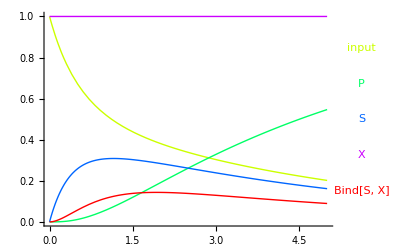

{{input→InterpolatingFunction[{{0.,5.}},<>],P→InterpolatingFunction[{{0.,5.}},<>],S→InterpolatingFunction[{{0.,5.}},<>],X→InterpolatingFunction[{{0.,5.}},<>],Bind[S,X]→InterpolatingFunction[{{0.,5.}},<>]}}

```mathematica
run[m,
 "IC"-> {input-> 1, X-> 1}, 
"TimeSpan"-> 5, 
"Frozen"-> {X},
"Parameters"-> {d-> 0}, 
"plot"-> True
]
```

Instead of specifying an input for the reactang S, we want to keep it zero until such time that an input signal turns it on. We define a stimulus function:

```mathematica
stimulus[t_]:= Which[t < 10, 0, t < 15, 1, t >= 15, 0];
```

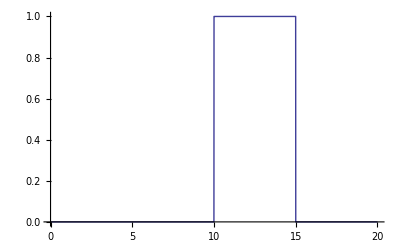

```mathematica
Plot[stimulus[t], {t, 0,20}]
```

run a simulation using the stimulus function for the variable “input”

use runPlot instead of automatic plotting to give more control over plots.

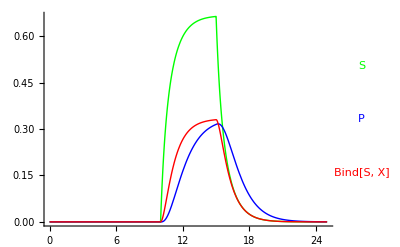

```mathematica
simulation = run[m, 
"IC" -> {X -> 1}, 
"TimeSpan" -> 25,"BoundaryConditions" -> {input[t] -> stimulus[t]},
   frozen -> {X}];
runPlot[simulation, {S,P, Bind[S,X]}]
```

Use manipulate to play with some of the parameters and initial conditions.

```mathematica
Manipulate[
Block[{s},
s=run[{{Overscript[S⇄P, X],k1,k2,k3},{P->∅,d},{input⇄S,k3,k4}}, 
"IC" -> {X -> X0}, 
"TimeSpan" -> 25,"BoundaryConditions" -> {input[t] -> stimulus[t]},
 frozen -> {X}];
runPlot[s, {S,P, Bind[S,X]}]
],
{{X0,1}, 0,10},
{{k1, 1}, 0, 10},
{{d, 0}, 0, 10}
]
```